```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Error while cosntraining u *)

CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[τ - t], xdot -> xdot1a[τ - t], θ ->θ1a[τ - t], θdot -> θdot1a[τ - t], u -> u1a[τ - t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,maxError_,uMax_,maxCount_,maxJ_,initGuess_]:=
Module[{InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
count = 0;
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
count = count+1;
];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]



testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:= Clip[uff[t]+ufb[t],{-uBound,uBound}];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];


J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

Manual implementation of periodic re-computations

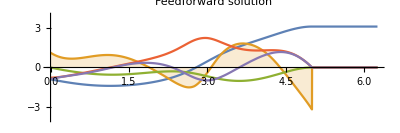

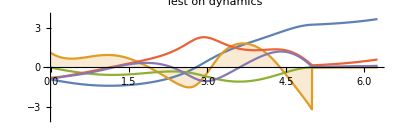

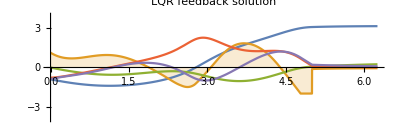

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 5;maxIter = 30;maxError = 0.01;uBound = 2;maxCount = 5;
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
maxJ = uBound^2*τ;
InitGuess = {0,0,0,0};
ICs = {0,xdotInit,θInit,θdotInit};
ICs = {0,-0.8972307770974721,-0.9070811023479912,-0.7842332462088191};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,uBound,maxCount,maxJ,InitGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound,K];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
τNew =τ/3;
θInit = θ1c[τNew] - Round[θ1c[τNew],2*π];
IC2 = {x1c[τNew],xdot1c[τNew],θInit,θdot1c[τNew]};
initGuess = {λ1ff0[τNew],λ2ff0[τNew],λ3ff0[τNew],λ4ff0[τNew]};
```

We were able to get this bad solution to the given well behaved solution after a few iterations.

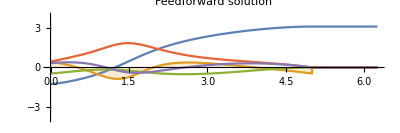

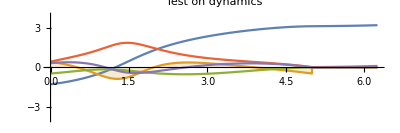

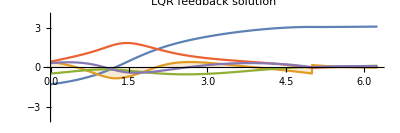

{-0.312335,-0.405951,0.801968,1.78988}

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 5;maxIter = 30;maxError = 0.01;uBound = 2;maxCount = 5;
ICs =IC2;
error = Norm[ICs - {0,0,π,0}];
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,uBound,maxCount,maxJ,InitGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound,K];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
τNew =τ/3;
θInit = θ1c[τNew] - Round[θ1c[τNew],2*π];
IC2 = {x1c[τNew],xdot1c[τNew],θInit,θdot1c[τNew]}
initGuess = {λ1ff0[τNew],λ2ff0[τNew],λ3ff0[τNew],λ4ff0[τNew]};
```

Periodic Re computations Skeleton Code

1

2

3

4

5

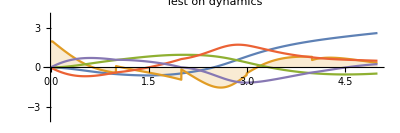

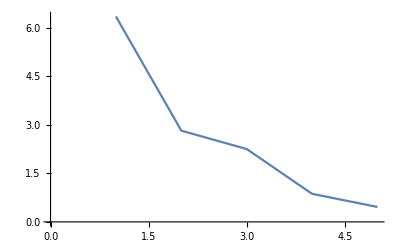

```mathematica
n = 50; τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 100;uBound = 2;maxCount = 7;
M =5; (*M is the no of times the solution will be recomputed in time τ  *)
A = 0.2;maxError = 0.01;
maxErrorInitial = 1;
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f]
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
ICs = {0,0,0,0};
xs[t_] := 0;
xdots[t_] := 0;
θs[t_] := 0;
θdots[t_] := 0;
Js = {};
errorInitial = 10;
initGuess = {0,0,0,0};
count = 0;
maxcountAlgo = 10;maxJ = uBound^2*τ;
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError ,uBound,maxCount,maxJ,initGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound,K]];
ICs = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};
errorInitial = Norm[ICs - {0,0,π,0}];
initGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
xs = MyAppend[xs, x1b, τ*count/M, τ*1/M];
xdots = MyAppend[xdots, xdot1b, τ*count/M, τ*1/M];
  θs = MyAppend[θs, θ1b, τ*count/M, τ*1/M];
θdots = MyAppend[θdots, θdot1b, τ*count/M, τ*1/M];
us = MyAppend[us, u1b, τ*count/M, τ*1/M];
Js = Append[Js,J];
count = count + 1;	
Print[count];	
]
p1a = Plot[{θs[t], us[t], xs[t], θdots[t], xdots[t]}, {t, 0, τ*1/M*count}, PlotRange -> {-4, 4}, Filling -> {2 -> Axis}, PlotLegends -> {"θ1b", "u1b", "x1b", "θdot1b", "xdot1b"}, PlotLabel -> "Test on dynamics", AspectRatio -> 1/3, ImageSize -> 400, GridLines -> {None, {-π, π}}];
p1b = ListLinePlot[Js];
Grid[{{p1a,p1b}}]
```

Problematic initial conditions

{0, -1.7176561578501914`, 1.9865343349458087`, -1.0173496185733697`} -- - Works with n = 50
{0, -1.3903695773492997`, 1.2310181542446177`, -0.6104047394312593`} ---- Works with n = 30
{0, 0.08036047668264246`, 1.3496547583989287`, 0.6830225774268248`}
{0, -0.6909899189385493`, 0.6897150795907763`, -0.7182564346929077`}

Periodic Re computations using previous estimate for costate

1

2

3

4

5

6

7

8

9

10

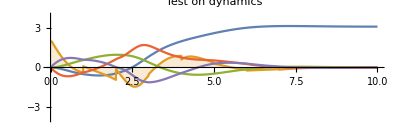

13.1313

```mathematica
n = 20; τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 30;uBound = 2;maxCount = 5;
M =5; (*M is the no of times the solution will be recomputed in time τ  *)
A = 0.2;maxError = 0.01;
maxErrorInitial = 1;
initialConditions = {0,0,0,0};
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f]

ICs = initialConditions;
xs[t_] := 0;
xdots[t_] := 0;
θs[t_] := 0;
θdots[t_] := 0;
Js = 0;
errorInitial = 10;
initGuess = {0,0,0,0};
count = 0;
maxcountAlgo = 10;
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError ,uBound,maxCount,initGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound]];
ICs = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};
initGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
xs = MyAppend[xs, x1b, τ*count/M, τ*1/M];
xdots = MyAppend[xdots, xdot1b, τ*count/M, τ*1/M];
  θs = MyAppend[θs, θ1b, τ*count/M, τ*1/M];
θdots = MyAppend[θdots, θdot1b, τ*count/M, τ*1/M];
us = MyAppend[us, u1b, τ*count/M, τ*1/M];
Js = Js + J;     
count = count + 1;	
Print[count];	
]
p1b = Plot[{θs[t], us[t], xs[t], θdots[t], xdots[t]}, {t, 0, τ*1/M*count}, PlotRange -> {-4, 4}, Filling -> {2 -> Axis}, PlotLegends -> {"θ1b", "u1b", "x1b", "θdot1b", "xdot1b"}, PlotLabel -> "Test on dynamics", AspectRatio -> 1/3, ImageSize -> 400, GridLines -> {None, {-π, π}}]
Js
```

Periodic Re computations without using previous estimate for costate

1

2

3

4

5

6

7

8

9

10

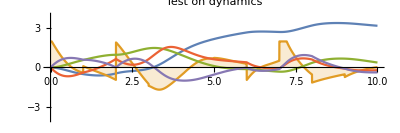

```mathematica
n = 20; τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 30;uBound = 2;maxCount = 5;
M =5; (*M is the no of times the solution will be recomputed in time τ  *)
A = 0.2;maxError = 0.01;
maxErrorInitial = 1;
initialConditions = {0,0,0,0};
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f]

ICs = initialConditions;
xs[t_] := 0;
xdots[t_] := 0;
θs[t_] := 0;
θdots[t_] := 0;
Js = 0;
errorInitial = 10;
initGuess = {0,0,0,0};
count = 0;
maxcountAlgo = 10;
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError ,uBound,maxCount,initGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uBound]];
ICs = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};
initGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
initGuess = {0,0,0,0};
xs = MyAppend[xs, x1b, τ*count/M, τ*1/M];
xdots = MyAppend[xdots, xdot1b, τ*count/M, τ*1/M];
  θs = MyAppend[θs, θ1b, τ*count/M, τ*1/M];
θdots = MyAppend[θdots, θdot1b, τ*count/M, τ*1/M];
us = MyAppend[us, u1b, τ*count/M, τ*1/M];
Js = Js + J;     
count = count + 1;	
Print[count];	
]
p1b = Plot[{θs[t], us[t], xs[t], θdots[t], xdots[t]}, {t, 0, τ*1/M*count}, PlotRange -> {-4, 4}, Filling -> {2 -> Axis}, PlotLegends -> {"θ1b", "u1b", "x1b", "θdot1b", "xdot1b"}, PlotLabel -> "Test on dynamics", AspectRatio -> 1/3, ImageSize -> 400, GridLines -> {None, {-π, π}}]
Js
```

### Evaluate Robustness of MPC Variant wrt Model Mismatch

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

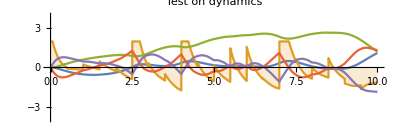
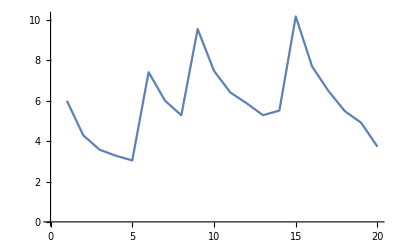
-Graphics- | -Graphics-

```mathematica
n = 20; τ = 5; τ1 = τ*1.25 ;order = 5;maxIter = 100;uBound = 2;maxCount = 7;
M =10; (*M is the no of times the solution will be recomputed in time τ  *)
A1 = 0;maxError = 0.01;
AError = 0.5;
A2 = A1 + AError;
maxErrorInitial = 1;
MyAppend[f1_, f2_, T1_, dT_] := Module[{f},
    f[t_] := Piecewise[{{f1[t], 0 <= t <= T1}, {f2[t - T1], T1 <= t <= T1 + dT}}];
    f]

ICs = {0,0,0,0};
xs[t_] := 0;
xdots[t_] := 0;
θs[t_] := 0;
θdots[t_] := 0;
Js = {};
errorInitial = 10;
initGuess = {0,0,0,0};
count = 0;
maxcountAlgo = 20;maxJ = uBound^2*τ;
While[errorInitial > maxErrorInitial && count < maxcountAlgo,
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A1,order,maxIter,maxError ,uBound,maxCount,maxJ,initGuess]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A2,uBound,K]];
ICs = {x1b[τ*1/M], xdot1b[τ*1/M], θ1b[τ*1/M], θdot1b[τ*1/M]};
errorInitial = Norm[ICs - {0,0,π,0}];
initGuess = {λ1ff0[τ*1/M],λ2ff0[τ*1/M],λ3ff0[τ*1/M],λ4ff0[τ*1/M]};
xs = MyAppend[xs, x1b, τ*count/M, τ*1/M];
xdots = MyAppend[xdots, xdot1b, τ*count/M, τ*1/M];
  θs = MyAppend[θs, θ1b, τ*count/M, τ*1/M];
θdots = MyAppend[θdots, θdot1b, τ*count/M, τ*1/M];
us = MyAppend[us, u1b, τ*count/M, τ*1/M];
Js = Append[Js,J];
count = count + 1;	
Print[count];	
]
p1a = Plot[{θs[t], us[t], xs[t], θdots[t], xdots[t]}, {t, 0, τ*1/M*count}, PlotRange -> {-4, 4}, Filling -> {2 -> Axis}, PlotLegends -> {"θ1b", "u1b", "x1b", "θdot1b", "xdot1b"}, PlotLabel -> "Test on dynamics", AspectRatio -> 1/3, ImageSize -> 400, GridLines -> {None, {-π, π}}];
p1b = ListLinePlot[Js];
Grid[{{p1a,p1b}}]
```